All sections can be opened by mouse-click.

## Task 1

Goal: Predict IgG MFI against pertussis toxin (PT) at Day 14

### Upload Data: Antibody Titers

Load information into data variable of the form: data[{antigen,subject,time,isotype}]=MFI

```mathematica
(* Training data *)
rawDataSpecimenTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_specimen.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_specimen.tsv"}]};
rawDataAbTiterTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_plasma_ab_titer.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_plasma_ab_titer.tsv"}]};
(* Testing data *)
rawDataSpecimenTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_specimen.tsv"}]];
rawDataAbTiterTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_plasma_ab_titer.tsv"}]];
```

```mathematica
(* In 2020-21, only consider the IgG data available in 2022 *)
rawDataAbTiterTraining=Cases[rawDataAbTiterTraining,{_,Alternatives@@Union@rawDataAbTiterTesting[[All,2]],__}];
```

```mathematica
(* === Replacing MFI=0->0.01 in 2020 and MFI=0->0.1 in 2021-22 === *)
posReplace=Position[rawDataAbTiterTraining[[All,5]],0|0.];
rawDataAbTiterTraining[[Flatten@posReplace,5]]=0.1;
posReplace=Position[rawDataAbTiterTesting[[All,5]],0|0.];
rawDataAbTiterTesting[[Flatten@posReplace,5]]=0.1;
```

```mathematica
(* === Import testing data === *)
rawData=MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,3}]]&,MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,2}]]&,#[[{4,1,1,2,5}]]&/@rawDataAbTiterTesting,{All,2}],{All,3}];
(* Subjects in testing group *)
listSubjectsTesting=Union@rawData[[All,2]];
(* Times measured for each subject *)
Do[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}]
(* {Antigen,Isotype} measured for each subject *)
Do[
antigens[entry[[1,1]]]=Rest/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1,4}]],#[[{1,3,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]],entry[[4]]}]=entry[[-1]]
,{entry,rawData}]
```

```mathematica
(* === Import training data === *)
Block[{rep1=Rule@@@rawDataSpecimenTraining⟦All,{1,3}⟧,rep2=Rule@@@rawDataSpecimenTraining⟦All,{1,2}⟧},rawData=MapAt[#1/.rep1&,MapAt[#1/.rep2&,rawDataAbTiterTraining⟦All,{4,1,1,2,5}⟧,{All,2}],{All,3}]];
(* Remove antigens that are not in prediction dataset *)
rawData=DeleteCases[rawData,{antigen_,_,_,isotype_,_}/;!MemberQ[antigens[First@listSubjectsTesting],{antigen,isotype}]];
listSubjectsTraining=Union[rawData⟦All,2⟧];
(* Times measured for each subject *)
Do[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}]
(* {Antigen,Isotype} measured for each subject *)
Do[
antigens[entry[[1,1]]]=Rest/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1,4}]],#[[{1,3,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]],entry[[4]]}]=entry[[-1]]
,{entry,rawData}]
```

Note: There are a few IgG features missing from the 2020 data that are present in the 2021-2022 datasets. We will ignore these and hope they are not important for predictions [this can be checked on a subset of 2021 data]

```mathematica
UniqueElements[DeleteDuplicates[antigens/@listSubjectsTraining]]
```

{{},{{DT,IgG},{FIM2/3,IgG},{OVA,IgG},{TT,IgG}}}

```mathematica
(* Unify lists *)
listSubjects=Join[listSubjectsTraining,listSubjectsTesting];
```

```mathematica
(* Stratify by year *)
listSubjectsTraining2020=Cases[listSubjectsTraining,val_/;val<=60];
listSubjectsTraining2021=Cases[listSubjectsTraining,val_/;61<=val];
```

```mathematica
Clear[rawData,rawDataSpecimenTraining,rawDataAbTiterTraining,rawDataSpecimenTesting,rawDataAbTiterTesting]
```

#### Defining Critical Time Points

Many of the 2020 participants (Subjects #1-60, excluding #2 and #8) don’t have any Day 0 measurements, but they have a nearby time point. Most of the 2021 participants (Subjects #61-96, excluding # 82, 87, 88) have Day 0 values

Given these limited data, it seems reasonable that we should only use the Day 0 values (or whichever time points is closest) in the predictions, rather than bothering with the Day -14 or Day -30 values

```mathematica
(*ListPlot[Join@@(Tuples[{times[#],{#}}]&/@listSubjects),Frame->{True,True,False,False},PlotMarkers->plotMarker[0.02],FrameLabel->(font[#,14]&/@{"Days Post-Vac","Subject"}),PlotLabel->font["Ab Titer Measurements",16],PlotRange->{{All,15},Automatic}]*)
```

In 2022, we have multiple pre-vaccination time points for each participant. However, in all prior years there was only one pre-vaccination measurement, so we cannot use these other pre-vaccination time points to determine how stable the IgG and IgG1-4 measurements are

2020 participants only had one pre-vaccination timepoint (which wasn’t always consistent), so we cannot use them to compare

```mathematica
(*times/@Cases[listSubjects,val_/;val<=60]//Grid*)
```

2021 participants only had one pre-vaccination timepoint (almost always Day 0)

```mathematica
(*times/@Cases[listSubjects,val_/;61<=val<=96]//Grid*)
```

Given this setup, the best we can do is define the Day≤0 response as pre-vac and use it to predict the Day 14 (or the closest day to it) post-vac response

```mathematica
Do[
timePreVac[subject]=First@Cases[times[subject],val_/;val<=0];
timePostVac[subject]=First@Nearest[times[subject],14];
,{subject,listSubjectsTraining}]
```

```mathematica
Do[
timePreVac[subject]=Max@Cases[times[subject],val_/;val<=0];
,{subject,listSubjectsTesting}]
```

### Task 1.1: Absolute PT IgG Titer

#### Choose a model architecture by predicting between 2020↔2021 data

Use Rank Correlation as the metric. Predict in both directions (average of both correlations)

Start with the following simple model: Input PT IgG titers ∝ Output PT IgG titers

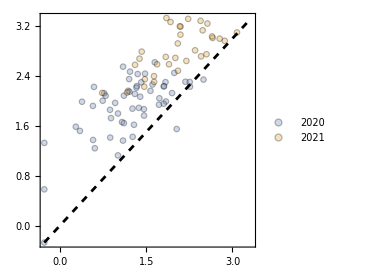

```mathematica
plotData=Table[
Log10@{data[{"PT",#,timePreVac[#],"IgG"}],data[{"PT",#,timePostVac[#],"IgG"}]}&/@listSubjects
,{listSubjects,{listSubjectsTraining2020,listSubjectsTraining2021}}];
plot[plotData,PlotLegends->{"2020","2021"}]
```

```mathematica
(* === 2020 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[data[{"PT",#,timePreVac[#],"IgG"}]&/@listSubjectsTraining2020];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[data[{"PT",#,timePostVac[#],"IgG"}]&/@listSubjectsTraining2020];
(* 2020 results *)
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[data[{"PT",#,timePreVac[#],"IgG"}]&/@listSubjectsTraining2021];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[data[{"PT",#,timePostVac[#],"IgG"}]&/@listSubjectsTraining2021];
(* 2021 results *)
res2021=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
```

0.60254

This basic model already does a decent job. Let’s embellish upon this result!

#### Finding the most predictive features

Determining what set of input features lead to the best model predictions. The idea is to start with the PT IgG feature (which we know is important) and then add the most-predictive additional feature until prediction accuracy no longer improves. After that, we will try to remove features one-at-a-time to see if any lead to further improvements in prediction accuracy.

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
(* Features available in all there years *)
listFeatures={{"PT","IgG"}};
potentialFeatures=Intersection@@(antigens/@listSubjects);
```

```mathematica
continue=True;
currentBest=test[listFeatures]
```

0.60254

```mathematica
Do[
If[continue,
newResults=Echo@ReverseSort@Table[
{test[Append[listFeatures,newFeature]],newFeature}
,{newFeature,potentialFeatures}]
];
If[newResults[[1,1]]>currentBest,
Echo[newResults[[1,2]],"Adding feature:"];
AppendTo[listFeatures,newResults[[1,2]]];
currentBest=newResults[[1,1]];
Echo[listFeatures,"Feature list:"];
potentialFeatures=DeleteCases[Intersection@@(antigens/@listSubjects),Alternatives@@listFeatures],
Echo[listFeatures,"No new feature benefits. Best result is:"];
continue=False
]
,{7}]
```

Note: In different runs, you can get slightly different feature sets, which is not promising. That suggests that we really should be running Predict multiple times to ensure a robust result.

Trying to remove bad features

```mathematica
continue=True;
listFeatures={{"PT","IgG"},{"DT","IgG2"},{"PT","IgG4"},{"FIM2/3","IgG2"},{"FIM2/3","IgG1"},{"FHA","IgG"},{"TT","IgG4"}};
currentBest=test[listFeatures]
```

```mathematica
Do[
If[continue,
newResults=Echo@ReverseSort@Table[
{test[Delete[listFeatures,removeIndex]],listFeatures[[removeIndex]]}
,{removeIndex,Length@listFeatures}]
];
If[newResults[[1,1]]>currentBest,
Echo[newResults[[1,2]],"Removing feature:"];
listFeatures=DeleteCases[listFeatures,newResults[[1,2]]];
currentBest=newResults[[1,1]];
Echo[listFeatures,"Feature list:"],
Echo[listFeatures,"No new feature benefits. Best result is:"];
continue=False
]
,{3}]
```

Try adding features once again to see if anything new arises
Conclusion: There are no new features that should be added

```mathematica
(* Features available in all there years *)
listFeatures={{"PT","IgG"},{"DT","IgG2"},{"PT","IgG4"},{"FIM2/3","IgG1"},{"FHA","IgG"},{"TT","IgG4"},{"FHA","IgG1"}};
continue=True;
currentBest=test[listFeatures]
```

```mathematica
Do[
If[continue,
newResults=Echo@ReverseSort@Table[
{test[Append[listFeatures,newFeature]],newFeature}
,{newFeature,potentialFeatures}]
];
If[newResults[[1,1]]>currentBest,
Echo[newResults[[1,2]],"Adding feature:"];
AppendTo[listFeatures,newResults[[1,2]]];
currentBest=newResults[[1,1]];
Echo[listFeatures,"Feature list:"];
potentialFeatures=DeleteCases[Intersection@@(antigens/@listSubjects),Alternatives@@listFeatures],
Echo[listFeatures,"No new feature benefits. Best result is:"];
continue=False
]
,{3}]
```

#### Comparing predictions models

```mathematica
listFeatures={{"PT","IgG"},{"DT","IgG2"},{"PT","IgG4"},{"FIM2/3","IgG1"},{"FHA","IgG"},{"TT","IgG4"},{"FHA","IgG1"},{"PT","IgG1"}};
```

Try using linear regression with regularization, as well as all other model types (but likely linear regression because we have so little data)

```mathematica
Clear[test]
test[listFeatures_,method_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->method];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->method];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
res=Table[{method,test[listFeatures,method]},{method,{Automatic,"DecisionTree","GradientBoostedTrees","LinearRegression","NearestNeighbors","NeuralNetwork","RandomForest","GaussianProcess"}}];
ReverseSortBy[res,Last]
```

Let’s see how much we can further improve LinearRegression
Conclusions: Doesn’t seem like regularization helps

```mathematica
res=Table[
{prop1,prop2,test[listFeatures,{"LinearRegression","L1Regularization"->prop1,"L2Regularization"->prop2(*,"OptimizationMethod"->prop3*)}]}
,{prop1,0.,0.5,0.1},{prop2,0.,1,0.2}(*,{prop3,{"NormalEquation","OrthantWiseQuasiNewton","StochasticGradientDescent"}}*)
];
ReverseSortBy[Join@@res,Last][[;;UpTo@10]]
```

Method doesn’t help either. Seems like plain vanilla linear regression works best

```mathematica
res=Table[
{prop3,test[listFeatures,{"LinearRegression","OptimizationMethod"->prop3}]}
,{prop3,{"NormalEquation","OrthantWiseQuasiNewton","StochasticGradientDescent"}}
];
ReverseSortBy[res,Last]
```

#### Final Model: Task 1.1

For the submission file, you rank the values from highest to lowest (i.e. highest = 1, lowest = N)

```mathematica
listFeatures={{"PT","IgG"},{"DT","IgG2"},{"PT","IgG4"},{"FIM2/3","IgG1"},{"FHA","IgG"},{"TT","IgG4"},{"FHA","IgG1"},{"PT","IgG1"}};
```

Try using linear regression with regularization, as well as all other model types (but likely linear regression because we have so little data)

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
test[listFeatures]
```

Final predictions: Let’s use use 2020→2022, since the 2021 pre-vaccination results are all substantially lower than the 2022 results.

```mathematica
(* === 2020->2022 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2022 data *)
dataTesting=Log10@N@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
(* Changing this to pre-vac so I can visualize how the post-vac predictions compare to the pre-vac values *)
data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTesting;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData={predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ;
```

```mathematica
(* Decent correlation between pre-vac values and post-vac predictions *)
plot[plotData]
```

```mathematica
ListPlot[First/@plotData]
```

Note: I just realized that Ordering sorts from smallest to largest, and I am supposed to be sorting from highest-to-lowest predicted titers. It shouldn’t effect the correlations (and hence any of the previous results), but I am fixing it here with a negative sign

```mathematica
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
exportData[[2;;,5]]=orderingPredict;
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

As a point of comparison, let’s see what the 2021 predictions look like

```mathematica
(*(* === 2021->2022 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2022 data *)
dataTesting=Log10@N@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
(* Changing this to pre-vac so I can visualize how the post-vac predictions compare to the pre-vac values *)
data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTesting;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData={predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ;*)
```

```mathematica
(*plot[plotData]*)
```

```mathematica
(*ListPlot[First/@plotData]
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]*)
```

These predictions suggest that there will be no vaccine response, which is clearly wrong. That said, the rankings are similar-ish [which goes to show that rankings can hide a lot of features in the data]. Still, we will proceed with the 2020→2022 predictions.

### Task 1.2: Fold Change of PT IgG Titer

#### Can pre-vac fold-change predict post-vac fold-change?

This time there appears to be an inverse correlation, much like an antibody ceiling effect. That means that a linear model is likely going to be the winner once again

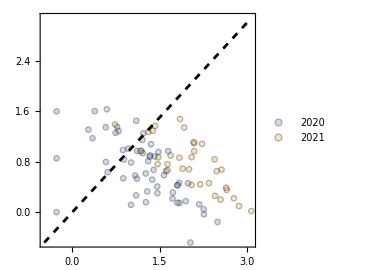

```mathematica
plotData=Table[
Log10@{data[{"PT",#,timePreVac[#],"IgG"}],data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]}&/@listSubjects
,{listSubjects,{listSubjectsTraining2020,listSubjectsTraining2021}}];
plot[plotData,PlotLegends->{"2020","2021"}]
```

#### Final Model: Task 1.2

```mathematica
listFeatures={{"PT","IgG"},{"PT","IgG4"},{"OVA","IgG1"}};
```

Standard predict with no mean centering

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2021;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2020;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
test[listFeatures]
```

Using 2020→2021, since 2020 seems so uniform

```mathematica
(* === 2020->2022 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2022 data *)
dataTesting=Log10@N@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
(* Changing this to pre-vac so I can visualize how the post-vac predictions compare to the pre-vac values *)
data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTesting;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData={predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ;
```

```mathematica
(* Seeing the expected negative correlation *)
plot[plotData]
```

```mathematica
ListPlot[First/@plotData]
```

```mathematica
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
exportData[[2;;,6]]=orderingPredict;
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

For comparison, let’s see what the 2021 predictions look like

```mathematica
(*(* === 2021->2022 === *)
dataTraining=Log10@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
data[{"PT",#,timePostVac[#],"IgG"}]/data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None,Method->"LinearRegression"];
(* Test on 2022 data *)
dataTesting=Log10@N@Append[
Table[
data[{feature[[1]],#,timePreVac[#],feature[[2]]}]
,{feature,listFeatures}],
(* Changing this to pre-vac so I can visualize how the post-vac predictions compare to the pre-vac values *)
data[{"PT",#,timePreVac[#],"IgG"}]]&/@listSubjectsTesting;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData={predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ;*)
```

Predictions also show the negative correlation. Very similar to the 2020 predictions, as expected

```mathematica
(*plot[plotData]*)
```

```mathematica
(*ListPlot[First/@plotData]
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]*)
```

## Task 2

Goal: Predict % live cells for Monocytes in the pbmc_cell_frequency files

### Upload Data: Cell Frequencies

Load information into data variable of the form
data[{antigen,subject,time}]=Percent Live Cell

```mathematica
(* Training data *)
rawDataSpecimenTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_specimen.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_specimen.tsv"}]};
rawDataCellFrequencyTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_pbmc_cell_frequency.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_pbmc_cell_frequency.tsv"}]};
(* Testing data *)
rawDataSpecimenTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_specimen.tsv"}]];
rawDataCellFrequencyTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_pbmc_cell_frequency.tsv"}]];
```

```mathematica
(* In 2020-21, only consider the cell types available in 2022 *)
rawDataCellFrequencyTraining=Cases[rawDataCellFrequencyTraining,{_,Alternatives@@Union@rawDataCellFrequencyTesting[[All,2]],__}];
```

```mathematica
(* === Import testing data === *)
rawData=MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,3}]]&,MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,2}]]&,#[[{2,1,1,-1}]]&/@rawDataCellFrequencyTesting,{All,2}],{All,3}];
```

```mathematica
(* Subjects in testing group *)
listSubjectsTesting=Union@rawData[[All,2]];
(* Times measured for each subject *)
Table[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}];
```

```mathematica
(* {Antigen,Isotype} measured for each subject *)
Do[
cells[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1}]],#[[{1,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]]}]=entry[[-1]]
,{entry,rawData}]
```

```mathematica
(* === Import training data === *)
Block[{rep1=Rule@@@rawDataSpecimenTraining⟦All,{1,3}⟧,rep2=Rule@@@rawDataSpecimenTraining⟦All,{1,2}⟧},rawData=MapAt[#1/.rep1&,MapAt[#1/.rep2&,rawDataCellFrequencyTraining⟦All,{2,1,1,-1}⟧,{All,2}],{All,3}]];
(* Remove cells that are not in prediction dataset *)
rawData=DeleteCases[rawData,{antigen_,_,_,isotype_,_}/;!MemberQ[cells[First@listSubjectsTesting],{antigen,isotype}]];
listSubjectsTraining=Union[rawData⟦All,2⟧];
(* Times measured for each subject *)
Do[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}]
(* {Antigen,Isotype} measured for each subject *)
Do[
cells[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1}]],#[[{1,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]]}]=entry[[-1]]
,{entry,rawData}]
```

```mathematica
(* Unify lists *)
listSubjects=Join[listSubjectsTraining,listSubjectsTesting];
```

```mathematica
(* Stratify by year *)
listSubjectsTraining2020=Cases[listSubjectsTraining,val_/;val<=60];
listSubjectsTraining2021=Cases[listSubjectsTraining,val_/;61<=val];
```

```mathematica
Clear[rawData,rawDataSpecimenTraining,rawDataCellFrequencyTraining,rawDataSpecimenTesting,rawDataCellFrequencyTesting]
```

#### Defining Critical Time Points

```mathematica
Do[
timePreVac[subject]=First@Cases[times[subject],val_/;val<=0];
timePostVac[subject]=First@Nearest[times[subject],1];
,{subject,listSubjectsTraining}]
```

```mathematica
Do[
timePreVac[subject]=Max@Cases[times[subject],val_/;val<=0];
,{subject,listSubjectsTesting}]
```

#### Dealing with Nan values

There are some nan values in 2021. Fortunately, most of them are at other timepoints (not pre-vac or Day 1 post-vac), but for Subject 70 we still have to care and remove them from the list of subjects

```mathematica
potentialFeatures=Intersection@@(cells/@listSubjects);
Cases[listSubjectsTraining2021,subject_/;!MatchQ[Append[
Table[data[{feature,subject,timePreVac[subject]}],{feature,potentialFeatures}],
data[{"Monocytes",subject,timePostVac[subject]}]],{_?NumericQ..}]]
```

{70}

```mathematica
listSubjectsTraining2021=DeleteCases[listSubjectsTraining2021,70];
listSubjectsTraining=DeleteCases[listSubjectsTraining,70];
```

Looking at the distributions of values

```mathematica
(*Table[
Histogram[Table[data[{"Monocytes",subject,timePreVac[subject]}],{subject,set}],{5},"Probability",PlotRange->{{0,50},Automatic}],{set,{listSubjectsTraining2020,listSubjectsTraining2021,listSubjectsTesting}}]*)
```

```mathematica
(*Table[
Histogram[Table[data[{"TemraCD4",subject,timePreVac[subject]}],{subject,set}],{1},"Probability",PlotRange->{{0,5},Automatic}],{set,{listSubjectsTraining2020,listSubjectsTraining2021,listSubjectsTesting}}]*)
```

```mathematica
(*Table[
Histogram[Table[data[{feature,subject,timePreVac[subject]}],{subject,set}],{5},"Probability",PlotRange->{{0,40},Automatic},PlotLabel->feature],{feature,{"Classical_Monocytes","CD8Tcells","NaiveCD8"}},{set,{listSubjectsTraining2020,listSubjectsTraining2021,listSubjectsTesting}}]*)
```

Fold-change of monocytes - it’s basically all the same, so there is no way I will be able to predict anything!

```mathematica
(*ListPlot@Table[data[{"Monocytes",subject,timePostVac[subject]}]/data[{"Monocytes",subject,timePreVac[subject]}],{subject,listSubjectsTraining}]*)
```

### Task 2.1: Absolute Frequency of Monocytes

#### Using Baseline Monocytes only

Baseline model: Input Monocytes at Day 0 = Output Monocytes at Day 1

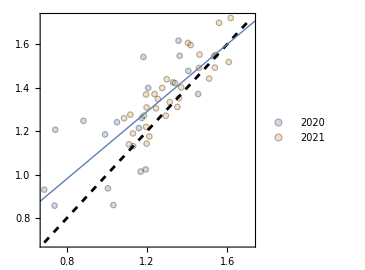

```mathematica
plotData=Table[
Log10@{data[{"Monocytes",#,timePreVac[#]}],data[{"Monocytes",#,timePostVac[#]}]}&/@listSubjects
,{listSubjects,{listSubjectsTraining2020,listSubjectsTraining2021}}];
Show[plot[plotData,PlotLegends->{"2020","2021"}],Plot[Evaluate@Fit[Join@@plotData,{1,x},x],{x,0,3},PlotStyle->Thick]]
```

```mathematica
(* === 2020 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[-data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2020];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[-data[{"Monocytes",#,timePostVac[#]}]&/@listSubjectsTraining2020];
(* 2020 results *)
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[-data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2021];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[-data[{"Monocytes",#,timePostVac[#]}]&/@listSubjectsTraining2021];
(* 2021 results *)
res2021=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
```

0.813788

This initial model already looks good, which is very promising!

#### Final Model: Task 2.1

```mathematica
listFeatures={"Monocytes","TemraCD4"};
```

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
test[listFeatures]
```

0.842624

Final predictions: Predict from 2021→2022 data, since the 2021 vs 2022 pre-vaccination Monocyte values are more similar than the 2020 vs 2022 values.

```mathematica
(* === 2021->2022 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None];
(* Predict 2022 data. Putting in the pre-vac Monocyte values as a comparison *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTesting;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
```

{11,19,5,7,12,2,6,18,4,16,13,10,14,3,1,9,15,17,8,21,20}

```mathematica
(*(* Decent correlation between pre-vac values and post-vac predictions *)
plot[plotData]*)
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
exportData[[2;;,7]]=orderingPredict;
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

### Task 2.2: Fold-Change Frequency of Monocytes

#### Using Baseline Monocytes only

Baseline model: Input Monocytes at Day 0 = Output Monocytes at Day 1

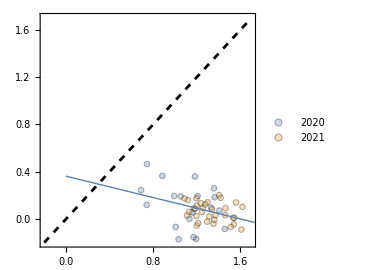

```mathematica
plotData=Table[
Log10@{data[{"Monocytes",#,timePreVac[#]}],data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]}&/@listSubjects
,{listSubjects,{listSubjectsTraining2020,listSubjectsTraining2021}}];
Show[plot[plotData,PlotLegends->{"2020","2021"},PlotRange->{-0.2,1.7}],Plot[Evaluate@Fit[Join@@plotData,{1,x},x],{x,0,3},PlotStyle->Thick]]
```

```mathematica
(*Table[
plotData=Table[
Log10@{data[{feature,#,timePreVac[#]}],data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]}&/@listSubjects
,{listSubjects,{listSubjectsTraining2020WP,listSubjectsTraining2020AP,listSubjectsTraining2021WP,listSubjectsTraining2021AP}}];
Show[plot[plotData,PlotLegends->{"2020 WP","2020 AP","2021 WP","2021 AP"},PlotRange->{-0.2,1.7},PlotLabel->feature],Plot[Evaluate@Fit[Join@@plotData,{1,x},x],{x,0,3},PlotStyle->Thick]]
,{feature,Intersection@@(cells/@listSubjects)}]*)
```

```mathematica
(* === 2020 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[-data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2020];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2020];
(* 2020 results *)
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021 === *)
(* For each person (in order), list the expected rank of their post-vac titers *)
orderingPredict=InversePermutation@Ordering[-data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2021];
(* Their actual rank *)
orderingActual=InversePermutation@Ordering[data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]&/@listSubjectsTraining2021];
(* 2021 results *)
res2021=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
```

0.261274

This will be more difficult, since nearly all of the values have a constant fold change≈1.

#### Final Model: Task 2.2

Alas, I could not find a good predictor here!

```mathematica
listFeatures={"Classical_Monocytes","CD8Tcells","NaiveCD8"};
```

Standard predict, no mean centering

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=0;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2021;
mean=0;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=0;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2020;
mean=0;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
test[listFeatures]
```

0.434958

Initially planned to use 2021→2022, since its pre-vac values are (perhaps slightly) closer to 2022’s pre-vac values
Conclusions: Unfortunately, this model’s predictions are completely flat...so I’m not using this.

```mathematica
(* === 2021->2022 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=0;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None];
(* Test on 2022 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTesting;
mean=0;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
plot[plotData]
```

Instead, using 2020→2022 which at least gives some scatter in its predictions, albeit still not a very promising result

{7,10,8,19,16,12,21,2,17,14,5,15,3,1,9,18,6,20,11,4,13}

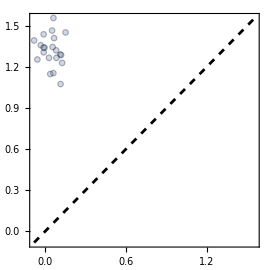

```mathematica
(* === 2020->2022 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePostVac[#]}]/data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=0;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None];
(* Test on 2022 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{"Monocytes",#,timePreVac[#]}]]&/@listSubjectsTesting;
mean=0;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
plot[plotData]
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
exportData[[2;;,8]]=orderingPredict;
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

## Task 3

Goal: Predict tpm of ENSG00000277632.1 (which stands for CCL3)

### Upload Data: Gene Expression

Note: To save on space, we removed the large gene expression files. Hence, to let the code below run, you will need to:

Download from the testing data the file 2022BD_pbmc_gene_expression.tsv and add it to Testing Data within this GitHub folder

Download from the training data the files 2020LD_pbmc_gene_expression.tsv and 2021LD_pbmc_gene_expression.tsv and add both to Training Data within this GitHub folder

Load information into data variable of the form
data[{geneID,subject,time}]=TPM

Since gene expression is a huge file, we decided to forgo the systematic feature search that we did in Tasks 1-2 and only search on a very limited set of genes. Specifically, we looked at every gene whose name starts with “ENSG0000027763”, which includes the gene-of-interest (ENSG00000277632.1) as well as 7 other genes with similar names.

It turns out that most of these genes only have TPM=0 (making them useless features), but one other gene (ENSG00000277634.1) had non-trivial values. Hence, we ended up only using these two genes to predict the post-vaccination response

```mathematica
(* Training data *)
rawDataSpecimenTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_specimen.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_specimen.tsv"}]};
rawDataGeneExpressionTraining=Join@@Rest/@Import/@{FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2020LD_pbmc_gene_expression.tsv"}],FileNameJoin[{ParentDirectory@NotebookDirectory[],"Training Data","2021LD_pbmc_gene_expression.tsv"}]};
(* Testing data *)
rawDataSpecimenTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_specimen.tsv"}]];
rawDataGeneExpressionTesting=Rest@Import[FileNameJoin[{ParentDirectory@NotebookDirectory[],"Testing Data","2022BD_pbmc_gene_expression.tsv"}]];
```

```mathematica
(* For simplicity, restrict ourselves to a very limited set of genes 27763X *)
rawDataGeneExpressionTraining=Cases[rawDataGeneExpressionTraining,{str_,__}/;StringMatchQ[str,"ENSG0000027763"~~__]];
rawDataGeneExpressionTesting=Cases[rawDataGeneExpressionTesting,{str_,__}/;StringMatchQ[str,"ENSG0000027763"~~__]];
```

```mathematica
(* Gene that we want to predict *)
geneOfInterest="ENSG00000277632.1";
```

```mathematica
(* === Import testing data === *)
rawData=MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,3}]]&,MapAt[#/.Rule@@@rawDataSpecimenTesting[[All,{1,2}]]&,#[[{1,2,2,-1}]]&/@rawDataGeneExpressionTesting,{All,2}],{All,3}];
```

```mathematica
(* Subjects in testing group *)
listSubjectsTesting=Union@rawData[[All,2]];
(* Times measured for each subject *)
Table[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}];
```

```mathematica
(* {Antigen,Isotype} measured for each subject *)
Do[
genes[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1}]],#[[{1,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]]}]=entry[[-1]]
,{entry,rawData}]
```

```mathematica
(* === Import training data === *)
Block[{rep1=Rule@@@rawDataSpecimenTraining⟦All,{1,3}⟧,rep2=Rule@@@rawDataSpecimenTraining⟦All,{1,2}⟧},rawData=MapAt[#1/.rep1&,MapAt[#1/.rep2&,rawDataGeneExpressionTraining⟦All,{1,2,2,-1}⟧,{All,2}],{All,3}]];
(* Remove genes that are not in prediction dataset *)
rawData=DeleteCases[rawData,{gene_,_,_,_}/;!MemberQ[genes[First@listSubjectsTesting],gene]];
listSubjectsTraining=Union[rawData⟦All,2⟧];
(* Times measured for each subject *)
Do[
times[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[Union@rawData[[All,{2,3}]],First]}]
(* {Antigen,Isotype} measured for each subject *)
Do[
genes[entry[[1,1]]]=Last/@entry
,{entry,GatherBy[SortBy[Union@rawData[[All,{2,1}]],#[[{1,2}]]&],First]}]
(* Import *)
Do[
data[{entry[[1]],entry[[2]],entry[[3]]}]=entry[[-1]]
,{entry,rawData}]
```

```mathematica
(* Unify lists *)
listSubjects=Join[listSubjectsTraining,listSubjectsTesting];
```

```mathematica
(* Stratify by year *)
listSubjectsTraining2020=Cases[listSubjectsTraining,val_/;val<=60];
listSubjectsTraining2021=Cases[listSubjectsTraining,val_/;61<=val];
```

#### Defining Critical Time Points

```mathematica
Do[
timePreVac[subject]=First@Cases[times[subject],val_/;val<=0];
timePostVac[subject]=First@Nearest[times[subject],1];
,{subject,listSubjectsTraining}]
```

```mathematica
Do[
timePreVac[subject]=Max@Cases[times[subject],val_/;val<=0];
,{subject,listSubjectsTesting}]
```

#### Distributions of values

It is immediately clear that:

Many of these genes are useless, since they all have TPM=0. We could hypothetically filter out all such genes from the entire list

```mathematica
Table[
Histogram[Table[data[{geneOfInterest,subject,timePreVac[subject]}],{subject,set}],{5},"Probability",PlotRange->{{0,300},Automatic}],{set,{listSubjectsTraining2020,listSubjectsTraining2021,listSubjectsTesting}}]
```

```mathematica
listGenesPotential={"ENSG00000277632.1","ENSG00000277634.1"};
```

```mathematica
Table[
Histogram[Table[data[{feature,subject,timePreVac[subject]}],{subject,set}],{5},"Probability",PlotRange->{{0,All},Automatic},PlotLabel->feature],{feature,listGenesPotential(*genes@listSubjects[[1]]*)},{set,{listSubjectsTraining2020,listSubjectsTraining2021,listSubjectsTesting}}]
```

Pre-vac vs post-vac CCL expression

```mathematica
plot[{Table[Log10@{data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePostVac[subject]}]},{subject,listSubjectsTraining2020AP}],Table[Log10@{data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePostVac[subject]}]},{subject,listSubjectsTraining2020WP}],Table[Log10@{data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePostVac[subject]}]},{subject,listSubjectsTraining2021AP}],Table[Log10@{data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePostVac[subject]}]},{subject,listSubjectsTraining2021WP}]},PlotLegends->{"2020 AP","2020 WP","2021 AP","2021 WP"}]
```

CCL fold-change

```mathematica
plot@Table[Log10@{data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePostVac[subject]}]/data[{geneOfInterest,subject,timePreVac[subject]}]},{subject,listSubjectsTraining}]
```

### Task 3.1: Absolute Gene Expression

#### Using gene-of-interest only

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
test[{geneOfInterest}]
```

#### Final Model: Task 3.1

Using two genes (un-logged)

Using 2021→2022, since this has a more similar pre-vac gene-of-interest profile than 2020→2022

```mathematica
listFeatures={"ENSG00000277632.1","ENSG00000277634.1"};
```

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2021;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2020;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
test[listFeatures]
```

Final predictions:

```mathematica
(* === 2021->2022 === *)
dataTraining=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=Mean@#[[;;-2]]&/@dataTraining;
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Predict 2022 data *)
dataTesting=(*Log10@*)Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
(* Changed to pre-vac, as always, to be able to plot predictions *)
data[{geneOfInterest,#,timePreVac[#]}]]&/@listSubjectsTesting;
mean=Mean@#[[;;-2]]&/@dataTesting;
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData]
```

```mathematica
plot[Log10@plotData]
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
```

```mathematica
exportData[[2;;,9]]=orderingPredict;
```

```mathematica
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

### Task 3.2: Gene Expression Fold-Change

#### Using gene-of-interest only

```mathematica
Clear[test]
test[listFeatures_]:=Block[{},
(* === 2020->2021 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]/data[{geneOfInterest,#,timePreVac[#]}]]&/@listSubjectsTraining2020;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2021 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]/data[{geneOfInterest,#,timePreVac[#]}]]&/@listSubjectsTraining2021;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === 2021->2020 === *)
dataTraining=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]/data[{geneOfInterest,#,timePreVac[#]}]]&/@listSubjectsTraining2021;
(* Mean-center using just the input data (not the output) *)
mean=0(*Mean@#[[;;-2]]&/@dataTraining*);
dataTrainingNormalized=dataTraining-mean;
predict=Predict[dataTrainingNormalized[[All,;;-2]]->dataTrainingNormalized[[All,-1]],TrainingProgressReporting->None(*,Method->"DecisionTree"*)];
(* Test on 2020 data *)
dataTesting=Log10@Append[
Table[data[{feature,#,timePreVac[#]}],{feature,listFeatures}],
data[{geneOfInterest,#,timePostVac[#]}]/data[{geneOfInterest,#,timePreVac[#]}]]&/@listSubjectsTraining2020;
mean=0(*Mean@#[[;;-2]]&/@dataTesting*);
plotData=Cases[{predict/@(dataTesting[[All,;;-2]]-mean)+mean,dataTesting[[All,-1]]}ᵀ,{_?NumericQ..}];
(* Predicted rank *)
orderingPredict=InversePermutation@Ordering[-First/@plotData];
(* Actual actual rank *)
orderingActual=InversePermutation@Ordering[-Last/@plotData];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
(* === Average over both years === *)
Mean[{res2020,res2021}]
]
```

```mathematica
test[{geneOfInterest}]
```

Surprisingly, the null model (shown below) does better, so we’re going with that

```mathematica
orderingPredict=InversePermutation@Ordering[Table[data[{geneOfInterest,subject,timePreVac[subject]}],{subject,listSubjectsTraining2020}]];
orderingActual=InversePermutation@Ordering[-Table[data[{geneOfInterest,subject,timePostVac[subject]}]/data[{geneOfInterest,subject,timePreVac[subject]}],{subject,listSubjectsTraining2020}]];
res2020=Correlation@@N[{orderingPredict,orderingActual}];
orderingPredict=InversePermutation@Ordering[Table[data[{geneOfInterest,subject,timePreVac[subject]}],{subject,listSubjectsTraining2021}]];
orderingActual=InversePermutation@Ordering[-Table[data[{geneOfInterest,subject,timePostVac[subject]}]/data[{geneOfInterest,subject,timePreVac[subject]}],{subject,listSubjectsTraining2021}]];
res2021=Correlation@@N[{orderingPredict,orderingActual}];
Mean[{res2020,res2021}]
```

#### Final Model: Task 3.2

Using the simplest possible “antibody ceiling” model, assuming that the higher your initial gene expression, the lower your fold-change

Final predictions:

```mathematica
plotData=Table[{1/data[{geneOfInterest,subject,timePreVac[subject]}],data[{geneOfInterest,subject,timePreVac[subject]}]},{subject,listSubjectsTesting}]
```

```mathematica
orderingPredict=InversePermutation@Ordering[-First/@plotData]
```

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}]];
exportData[[2;;,10]]=orderingPredict;
exportData//Grid
```

```mathematica
SystemOpen@Export[FileNameJoin[{NotebookDirectory[],"2024 - 2nd Prediction Challenge.tsv"}],exportData,"TextDelimiters"->""]
```

# Initialization

```mathematica
(* Example: fromDigits/@{"D","AA","BC"} *)
fromDigits[letters_]:=FromDigits[Flatten@List@LetterNumber[letters],26]
```

#### Plot Markers

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[],
"Diamond",Rotate[Rectangle[],π/4]
]}],size};
```

```mathematica
Options[markerAb]={"Opacity"->1,"Thickness"->0.02,"AspectRatio"->1};
markerAb[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,segLarge=,segSmall=,opacity=OptionValue["Opacity"],thickness=OptionValue["Thickness"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
segLarge=MapAt[aspect#&,segLarge,{All,2}];
segSmall=MapAt[aspect#&,segSmall,{All,2}];
{Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],JoinForm["Round"],Thickness[thickness]}],FilledCurve/@Line/@{segLarge,{-1,1}#&/@segLarge,segSmall,{-1,1}#&/@segSmall}}],size}
]
```

```mathematica
Options[markerVirus]={"Thickness"->0.015,"Thickness2"->0.015,"Opacity"->0.7,"OpacityFaceFormFactor"->0.8,"AspectRatio"->1,"GlowColor"->None};
markerVirus[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,thickness=Thickness[OptionValue["Thickness"]],thickness2=Thickness[OptionValue["Thickness2"]],
glowColor=OptionValue["GlowColor"],opacity=OptionValue["Opacity"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
{Graphics[{Opacity[opacity OptionValue["OpacityFaceFormFactor"]],
If[glowColor=!=None,{FaceForm[],EdgeForm[glowColor],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}]},{}],
EdgeForm[{thickness2,Opacity[opacity],Black}],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}],Disk[{0,0},0.7{1,aspect}],{Black,Opacity[opacity],thickness,Circle[{0,0},0.7{1,aspect}]}}],size}
]
```

#### Plot with Aspect Ratio → 1

Options:

"MarginalHistogram"->True shows histograms of the x- and y-coordinates of the data, with "MarginalHistogramBins" providing control of bin size using standard Histogram options

```mathematica
ClearAll[plot]
With[{extraOpts={"ShowFoldError"->None,
(* Plot best-perpendicular-fit line *)
"ShowBestFitLine"->False,
(* Options for marginal histograms *)
"MarginalHistogram"->False,"MarginalHistogramBins"->{Automatic,Automatic},
"MarginalHistogramPlotRange"->{Automatic,Automatic},
"MarginalHistogramAxisLabel"->(*None*)font["Count"],
PerformanceGoal->"Speed"
}},
Options[plot]=Join[extraOpts,Options@ListPlot];
SetOptions[plot,PlotMarkers->plotMarker[0.05,0.3],PlotRange->Automatic];
plot[rawData_,options:OptionsPattern[]]:=Block[{
showFit=OptionValue["ShowBestFitLine"],
showError=OptionValue["ShowFoldError"],
marginalHist=OptionValue["MarginalHistogram"],
histBins=OptionValue["MarginalHistogramBins"],
histLabel=OptionValue["MarginalHistogramAxisLabel"],
plotRange=OptionValue[PlotRange],
histPlotRange=OptionValue["MarginalHistogramPlotRange"],
plotStyle=OptionValue[PlotStyle],
performanceGoal=OptionValue[PerformanceGoal],
data,min,max,Δy,dataPlot,dataX,dataY,histX,histY},
data=rawData/.val:_LessThan|_GreaterThan:>First@val;
{min,max}=MinMax[DeleteMissing[data,If[MatchQ[data,{{_?NumberQ,_?NumberQ}..}],1,2],All]/.Around[val_,_]:>val];
plotRange=If[plotRange===Automatic,
ConstantArray[{min,max},2],
Switch[plotRange,
{_?NumericQ,_?NumericQ},{plotRange,plotRange},
{range_List,range_List},plotRange,
_,Echo["PlotRange must match along x and y","Warning!"];Return[$Failed]]
];
dataPlot=
Show[ListPlot[data,PlotRange->plotRange,Sequence@@DeleteCases[{options},Alternatives@@First/@extraOpts->_],ImageSize->270,AspectRatio->1,Frame->{True,True,False,False},FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers],Prolog->If[MatchQ[showError,{_?NumericQ,"Log"|"Linear"}],
Δy=If[Last@showError==="Log",Log10,Identity]@First@showError;
{{GrayLevel[0.9],Polygon[{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy},{plotRange[[1,1]],plotRange[[1,1]]-Δy}}]},{GrayLevel[0.7],Thickness[0.01],Line[{{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy}},{{plotRange[[1,1]],plotRange[[1,1]]-Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy}}}]}},{}](*,FrameTicks->ConstantArray[LinTicks[min,max,TickLengthScale->2],2]*)],Plot[Evaluate@If[showFit,
{x,fitPerp[DeleteMissing[data,1,All]]},
{x}
],{x,plotRange[[1,1]],plotRange[[1,2]]},PlotStyle->{{Black,Dashed},{Thick,If[plotStyle===Automatic,ColorData[97,1],plotStyle]}},Evaluate[Sequence@@DeleteCases[{options},Alternatives@@Join[First/@extraOpts,{DataRange,InterpolationOrder,IntervalMarkers,IntervalMarkersStyle,Joined,LabelingFunction,MaxPlotPoints,MultiaxisArrangement,PlotMarkers,PlotLegends}]->_]]]];
If[!marginalHist,
(* Only show data *)
dataPlot,
(* Also show marginal histograms *)
{dataX,dataY}=Transpose@data;
histX=Histogram[dataX,histBins[[1]],PlotRange->{histPlotRange[[1]],Automatic},Frame->{{True,False},{False,False}},FrameLabel->{None,histLabel},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
histY=Histogram[dataY,histBins[[2]],PlotRange->{Automatic,histPlotRange[[2]]},BarOrigin->Left,Frame->{{False,False},{True,False}},FrameLabel->{histLabel,None},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
ResourceFunction["PlotGrid"][{{histX,None},{Show[dataPlot,ImageSize->500],histY}},Spacings->5,ItemSize->{{200,100},{100,200}},AspectRatio->1]
]
]
]
```

```mathematica
(*(* Examples *)
SeedRandom[1];
plot[RandomReal[BinormalDistribution[{0,0},{1,1},0.5],100],"MarginalHistogram"->True]*)
```